# Differential Matrices for Levin’s Method

## K Integrals

```mathematica
Clear["Global'*"]
```

```mathematica
w={
k^2*SphericalBesselJ[l,α k]SphericalBesselJ[l,β k],
k^2*SphericalBesselJ[l+1,α k]SphericalBesselJ[l,β k],
k^2*SphericalBesselJ[l,α k]SphericalBesselJ[l+1,β k],
k^2*SphericalBesselJ[l+1,α k]SphericalBesselJ[l+1,β k]
};
```

```mathematica
dw=D[w,k]//FullSimplify;
```

```mathematica
Expand[dw]//TraditionalForm
```

{-α k^2 l+1k α lk β-β k^2 lk α l+1k β+2 k l lk α lk β+2 k lk α lk β,α k^2 lk α lk β-β k^2 l+1k α l+1k β,β k^2 lk α lk β-α k^2 l+1k α l+1k β,β k^2 l+1k α lk β+α k^2 lk α l+1k β-2 k l l+1k α l+1k β-2 k l+1k α l+1k β}

```mathematica
A={{2l/k,-α,-β,0},
{α,-2/k,0,-β},
{β,0,-2/k,-α},
{0, β,α,-2(l+2)/k}};
```

```mathematica
A//MatrixForm
```

((2 l)/k | -α | -β | 0
α | -2/k | 0 | -β
β | 0 | -2/k | -α
0 | β | α | -(2 (2+l))/k)

```mathematica
B={{2(1+l)/k,-α ,-β , 0},
{α , 0 ,0,-β },
{β , 0,0, -α },
{0, β , α , -2(1+l)/k}};
B//MatrixForm
```

((2 (1+l))/k | -α | -β | 0
α | 0 | 0 | -β
β | 0 | 0 | -α
0 | β | α | -(2 (1+l))/k)

```mathematica
dw==B.w//FullSimplify//TraditionalForm
```

True

```mathematica
B.w
```

{2 k^3 (1+l) SphericalBesselJ[l,k α] SphericalBesselJ[l,k β]-k^4 α SphericalBesselJ[l,k β] SphericalBesselJ[1+l,k α]-k^4 β SphericalBesselJ[l,k α] SphericalBesselJ[1+l,k β],k^4 α SphericalBesselJ[l,k α] SphericalBesselJ[l,k β]-k^4 β SphericalBesselJ[1+l,k α] SphericalBesselJ[1+l,k β],k^4 β SphericalBesselJ[l,k α] SphericalBesselJ[l,k β]-k^4 α SphericalBesselJ[1+l,k α] SphericalBesselJ[1+l,k β],k^4 β SphericalBesselJ[l,k β] SphericalBesselJ[1+l,k α]+k^4 α SphericalBesselJ[l,k α] SphericalBesselJ[1+l,k β]-2 k^3 (1+l) SphericalBesselJ[1+l,k α] SphericalBesselJ[1+l,k β]}

```mathematica
A//MatrixForm
```

(2/k | -5 | -5 | 0
5 | -2/k | 0 | -5
5 | 0 | -2/k | -5
0 | 5 | 5 | -6/k)

```mathematica
({{(2 l)/k, -α, -β, 0}, {α, -2/k, 0, -β}, {β, 0, -2/k, -α}, {0, β, α, -(2 (2+l))/k}})
```

{{2/k,-5,-5,0},{5,-2/k,0,-5},{5,0,-2/k,-5},{0,5,5,-6/k}}

```mathematica
FullSimplify[Eigenvalues[A]]
```

{-2/k,-2/k,-(2 (1+√(4-25 k^2)))/k,(2 (-1+√(4-25 k^2)))/k}

```mathematica
X[t_] = {x[t],y[t],z[t],a[t]};
```

```mathematica
F=B/.{α->1,β->2,l->1,k->t}
```

{{4/t,-1,-2,0},{1,0,0,-2},{2,0,0,-1},{0,2,1,-4/t}}

```mathematica
system = {X'[t] == -F.X[t],x[1]==1,y[1]==0,z[1]==0,a[1]==0}
```

{{x'[t],y'[t],z'[t],a'[t]}=={-(4 x[t])/t+y[t]+2 z[t],2 a[t]-x[t],a[t]-2 x[t],(4 a[t])/t-2 y[t]-z[t]},x[1]==1,y[1]==0,z[1]==0,a[1]==0}

```mathematica
sol=DSolve[system,{x,y,z,a},t]
```

DSolve[{{x'[t],y'[t],z'[t],a'[t]}=={-(4 x[t])/t+y[t]+2 z[t],2 a[t]-x[t],a[t]-2 x[t],(4 a[t])/t-2 y[t]-z[t]},x[1]==1,y[1]==0,z[1]==0,a[1]==0},{x,y,z,a},t]

```mathematica
sol =NDSolve[system,{x,y,z,a},{t,1,1000}]
```

{{x→InterpolatingFunction[{{1., 1000.}}, <>],y→InterpolatingFunction[{{1., 1000.}}, <>],z→InterpolatingFunction[{{1., 1000.}}, <>],a→InterpolatingFunction[{{1., 1000.}}, <>]}}

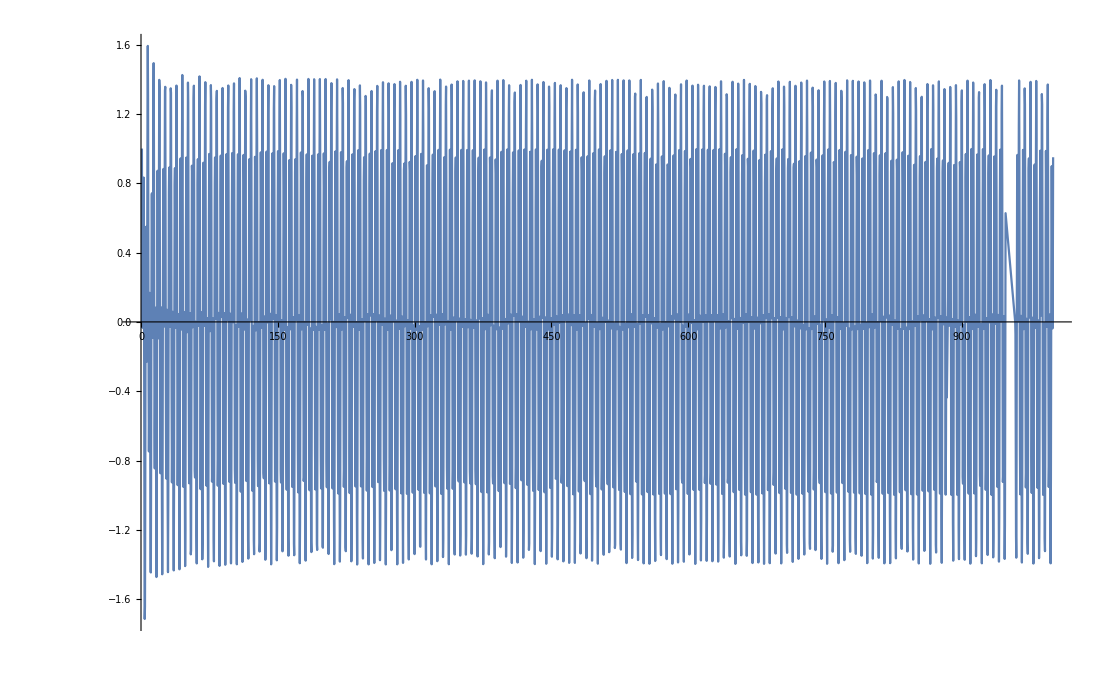

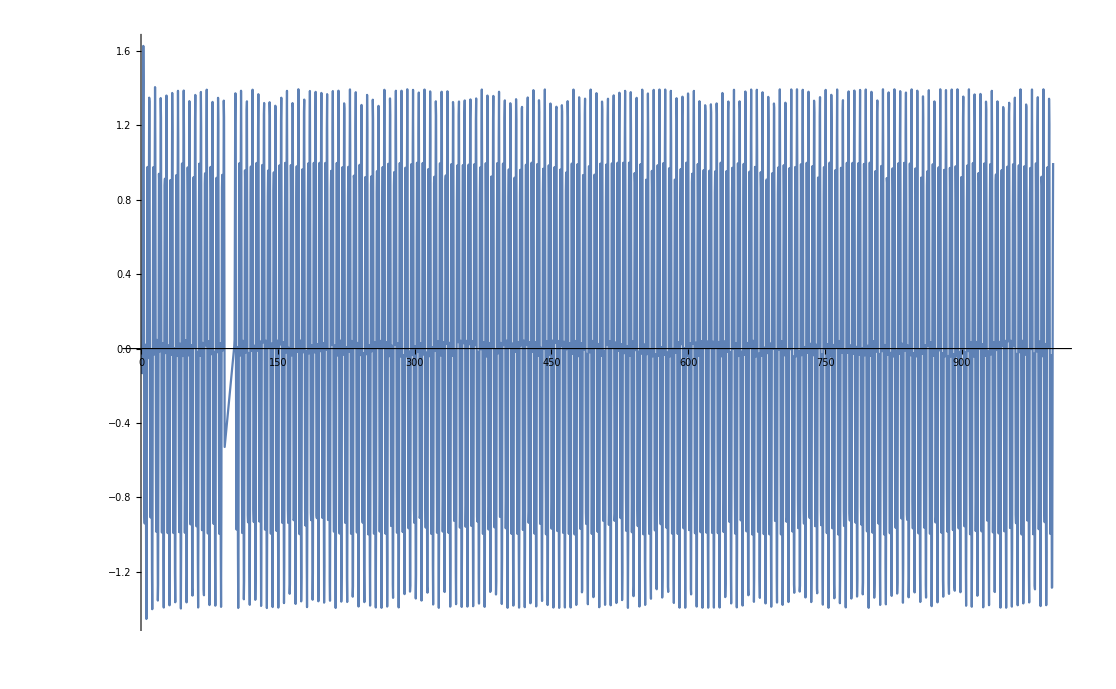

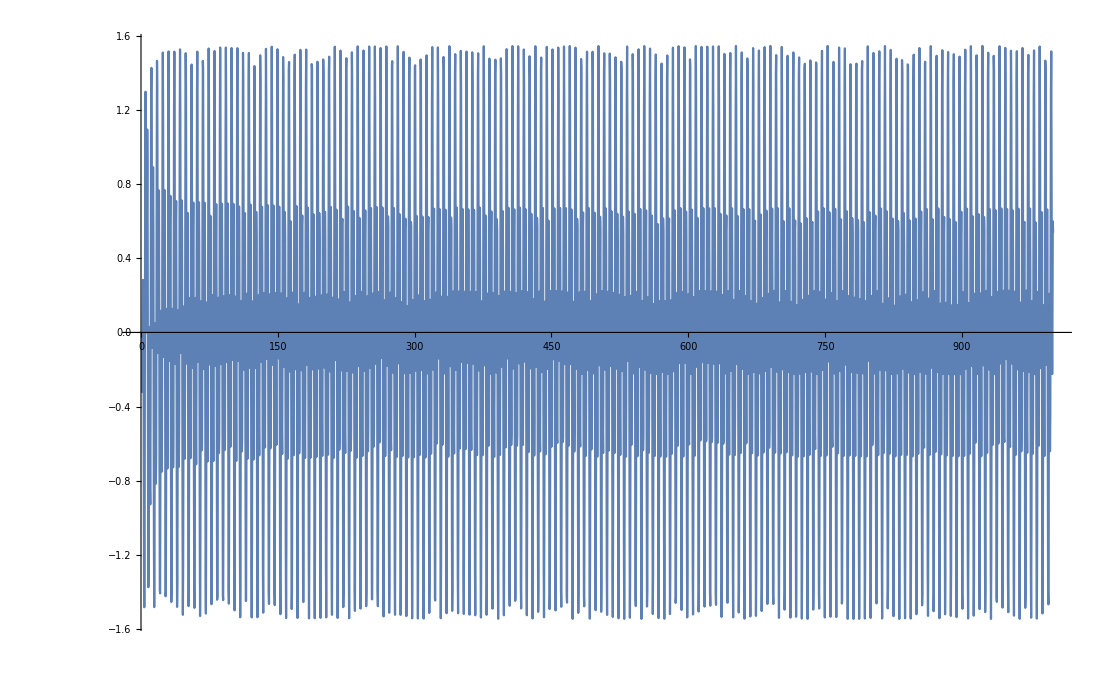

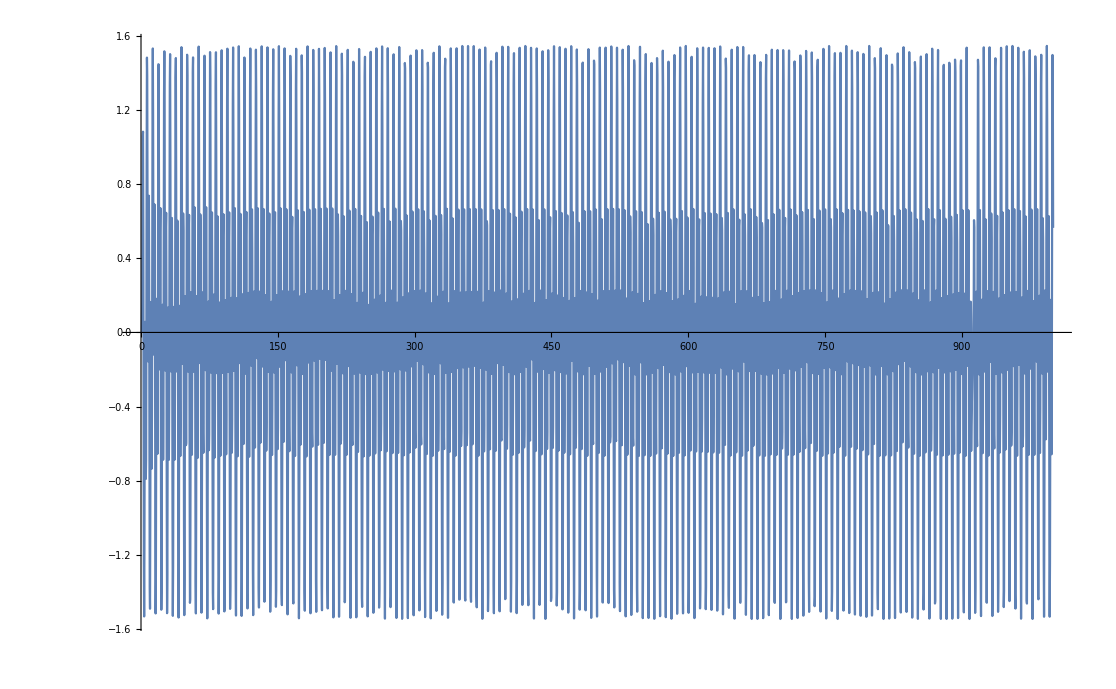

```mathematica
Plot[Evaluate[{x[t]}/.sol],{t,1,1000},PlotRange->Automatic]
Plot[Evaluate[{y[t]}/.sol],{t,1,1000},PlotRange->Automatic]
Plot[Evaluate[{z[t]}/.sol],{t,1,1000},PlotRange->Automatic]
Plot[Evaluate[{a[t]}/.sol],{t,1,1000},PlotRange->Automatic]
```

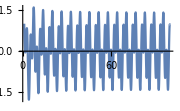

```mathematica
Show[%37,ImageSize->Small]
```

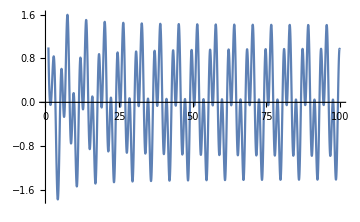

```mathematica
Show[%37,ImageSize->Medium]
```

```mathematica
Plot[Evaluate[{a[t]}/.sol],{t,1,100}]
```

NDSolve::ndode: The equations {1[1]==0} are not differential equations or initial conditions in the dependent variables {x,y,z}.

ReplaceAll::reps: {NDSolve[{{x'[t],y'[t],z'[t],0}=={-2 Power[«2»] x[«1»]+5 y[«1»]+5 z[«1»],5 1[«1»]-x[«1»]+2 Power[«2»] y[«1»],5 1[«1»]-x[«1»]+2 Power[«2»] z[«1»],6 Power[«2»] 1[«1»]-y[«1»]-z[«1»]},x[1]==1,y[1]==0,z[1]==0,1[1]==0},{x,y,z,1},{t,1,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.00202 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{{x'[1.00202],y'[1.00202],z'[1.00202],0}=={-1.99596 x[«1»]+5 y[«1»]+5 z[«1»],5 1[«1»]-x[«1»]+1.99596 y[«1»],5 1[«1»]-x[«1»]+1.99596 z[«1»],5.98789 1[«1»]-y[«1»]-z[«1»]},x[1]==1,y[1]==0,z[1]==0,1[1]==0},{x,«3»},{«19»,1,100}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.00202 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{«1»},{x,y,z,1.},{1.00202,1.,100.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 3.02243 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

```mathematica
Plot[sol.x,{t,1,100}]
```

NDSolve::dsvar: 1.00202 cannot be used as a variable.

NDSolve::dsvar: 3.02243 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

0.0837103520350064

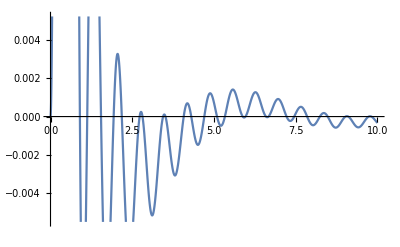

```mathematica
a=10^(-3);
b=10^(1);
α=4;
β=5;
l=1;
ans=NIntegrate[SphericalBesselJ[l,α k]SphericalBesselJ[l,β k],{k,a,b},Method->"LevinRule"];
NumberForm[ans,16]
Plot[SphericalBesselJ[l,α k]SphericalBesselJ[l,β k],{k,a,b}]
```

## H Integrals

```mathematica
w={
SphericalBesselJ[l,α k]^2,
SphericalBesselJ[l+1,α k]SphericalBesselJ[l,α k],
SphericalBesselJ[l+1,α k]^2
};
```

```mathematica
dw=D[w,k]//FullSimplify;
```

```mathematica
dw //TraditionalForm
```

{(2 15 k (sin(5 k)-2 15 k))/k,((5 k^2-3) (15 k)^2+8 k sinc(5 k) 15 k-1/5 sin^2(5 k))/k^2,2 25 k (5 15 k-(3 25 k)/k)}

```mathematica
A = {{2l/k, -2α, 0},
{α, -2/k,-α},
{0,2α,-2(l+2)/k}};
```

```mathematica
A//MatrixForm
```

(2/k | -10 | 0
5 | -2/k | -5
0 | 10 | -6/k)

```mathematica
dw==A.w//FullSimplify
```

True

```mathematica
True
a=1.0;
b=10.0;
α=0.01;
l=10;
ans=NIntegrate[k^6SphericalBesselJ[l,α k]^2,{k,a,b}];
NumberForm[ans,16]
```

True

1.958387322186554×10^-35

## I Integrals

```mathematica
w={
SphericalBesselJ[l,α k],
SphericalBesselJ[l+1,α k]
};
```

```mathematica
dw=D[w,k]//FullSimplify;
```

```mathematica
dw //TraditionalForm
```

{0.005 90.01 k-(0.5 100.01 k)/k-0.005 110.01 k,0.005 100.01 k-(0.5 110.01 k)/k-0.005 120.01 k}

```mathematica
A={{l/k,-α},
{α,-(l+2)/k}};
```

```mathematica
A//MatrixForm
```

(10/k | -0.01
0.01 | -12/k)

```mathematica
dw==A.w//FullSimplify
```

{0.005 SphericalBesselJ[9,0.01 k]-(10.5 SphericalBesselJ[10,0.01 k])/k+0.005 SphericalBesselJ[11,0.01 k],-0.005 SphericalBesselJ[10,0.01 k]+(11.5 SphericalBesselJ[11,0.01 k])/k-0.005 SphericalBesselJ[12,0.01 k]}=={0.,0.}

```mathematica
a=1.0;
b=10.0;
α=0.01;
l=10;
ans=NIntegrate[k^6SphericalBesselJ[l,α k],{k,a,b}];
NumberForm[ans,16]
```

4.277457293476394×10^-15

## Simultaneous Testing

```mathematica
a=10^(-3);
b=10^(1);
α=0.01;
β=10.0;
l=0;
```

```mathematica
ans=NIntegrate[SphericalBesselJ[l,α k]SphericalBesselJ[l,β k],{k,a,b}];
NumberForm[ans,16]
ans=NIntegrate[k^6*SphericalBesselJ[l,α k]^2,{k,a,b},Method->"LevinRule"];
NumberForm[ans,16]
ans=NIntegrate[k^6*SphericalBesselJ[l,α k],{k,a,b},Method->"LevinRule"];
NumberForm[ans,16]
```

0.1552239971513493

1.424871762830699×10^6

1.426720334142725×10^6